Constants:

```mathematica
Subscript[L, arm] = 0.25;
Subscript[d, ap] =  0.1542;
Subscript[d, pdp] = .2;
```

Takeup Analysis:
The take up equation is determined as follows

```mathematica
LTakeupSide[a_,Larm_, dpdp_, dap_] := Sqrt[(Larm Cos[a] - dap)^2 + (Larm Sin[a])^2] + Sqrt[(dap + dpdp - Larm Cos[a])^2 + (Larm Sin[a])^2] - dpdp;
LTakeup[a_, b_, Larm_, dpdp_, dap_] := LTakeupSide[a,Larm, dpdp, dap] + LTakeupSide[b,Larm, dpdp, dap];
```

```mathematica
Subscript[L, t] = LTakeup[a, b, Subscript[L, arm], Subscript[d, pdp], Subscript[d, ap]]
```

-0.3084+√((0.3542-0.25 Cos[a])^2+0.0625 Sin[a]^2)+√((-0.2+0.25 Cos[a])^2+0.0625 Sin[a]^2)+√((0.3542-0.25 Cos[b])^2+0.0625 Sin[b]^2)+√((-0.2+0.25 Cos[b])^2+0.0625 Sin[b]^2)

Sanity Check:
According to the cad, 109 degrees on both arms leads to about a 129 cm take-up. So our estimates are decently accurate (1.26).

```mathematica
LTakeup[109 * Pi / 180, 109 * Pi / 180, Subscript[L, arm], Subscript[d, pdp], Subscript[d, ap]]
```

1.25866

Plotting:

```mathematica
Plot3D[Subscript[L, t],{a,0,2 Pi},{b,0,2 Pi}, AxesLabel->{Subscript[α, 1], Subscript[α, 2], Subscript[L, takeup]}]
```

-Graphics3D-

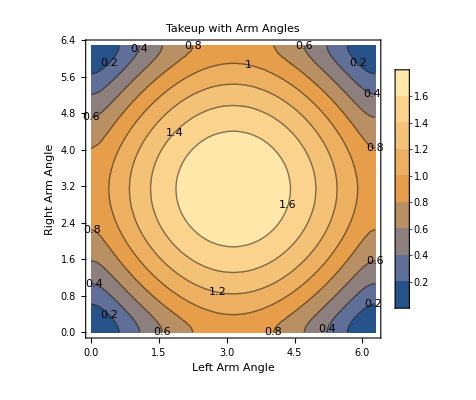

```mathematica
ContourPlot[Subscript[L, t], {a, 0, 2 * Pi}, {b, 0, 2 * Pi}, PlotLegends->Automatic, FrameLabel->{"Left Arm Angle","Right Arm Angle"}, PlotLabel -> "Takeup with Arm Angles", ContourLabels->(Text[Framed[#3],{#1,#2},BaseStyle->FontColor->Black]&)]
```

Required Take-up Analysis
These graphs were meant to go along with the shuttle automated required take-up determination procedure. It seems that if we spec the required takeup assuming the largest cable length we’re planning, the takeup isn’t too far off from the real value and it ensures we don’t hit the ground (though there may be problems with over tensioning). 

The first plot shows the difference between 10m and 26m cables and the second one plots the difference in required take up between the 10m and 26m cables.

Derivation (note that L_diff denotes the difference between stake span and cable length):

```mathematica
Subscript[H, droop] = 0.5;
```

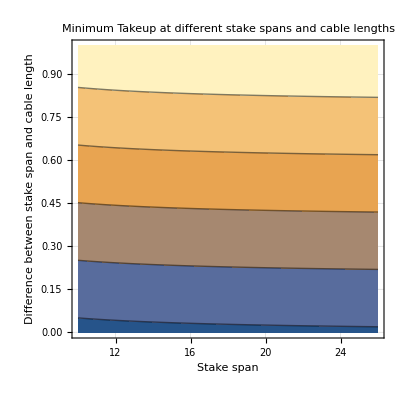

```mathematica
ContourPlot[x - Sqrt[4*(Subscript[H, droop] )^2 +(x - y)^2 ] && x > y, {x, 10,26}, {y, 0, 1}, GridLines -> Automatic, FrameLabel -> {"Stake span", "Difference between stake span and cable length"},PlotLabel -> "Minimum Takeup at different stake spans and cable lengths"]
```

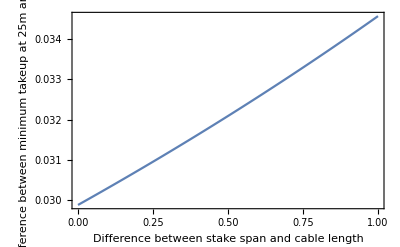

```mathematica
Plot[(25 - Sqrt[4*(Subscript[H, droop] )^2 +(25-x)^2 ]) - (10 - Sqrt[4*(Subscript[H, droop] )^2 +(10-x)^2 ]), {x, 0, 1}, Frame-> True, FrameLabel->{"Difference between stake span and cable length", "Difference between minimum takeup at 25m and 10m"}]
```